## Two kings

```mathematica
n=3;(*size of the board*)
```

```mathematica
kingMoves[x_,y_]:=Module[{ans={}},
If[x>1,
AppendTo[ans,{x-1,y}];
If[y>1,AppendTo[ans,{x-1,y-1}]];
If[y<n,AppendTo[ans,{x-1,y+1}]];
];
If[x<n,
AppendTo[ans,{x+1,y}];
If[y>1,AppendTo[ans,{x+1,y-1}]];
If[y<n,AppendTo[ans,{x+1,y+1}]];
];
If[y>1,AppendTo[ans,{x,y-1}]];
If[y<n,AppendTo[ans,{x,y+1}]];
ans
];(*returns a list of valid moves for a single king*)
```

```mathematica
validPosition[{{w1_,w2_},{b1_,b2_},m_}]:=!(Abs[w1-b1]<=1&&Abs[w2-b2]<=1);
(*{{white king x, white king y}, {black king x, black king y}, 1->white's move; 0->black's move}*)
```

```mathematica
nextPositions[{{w1_,w2_},{b1_,b2_},m_}]:=Module[{ans={}},
If[m==1,(*white's move*)
ans={#,{b1,b2},0}&/@kingMoves[w1,w2]
];
If[m==0,(*black's move*)
ans={{w1,w2},#,1}&/@kingMoves[b1,b2]
];
DeleteCases[ans,p_/; validPosition[p]==False]
];
```

```mathematica
edgesFromPosition[p_]:={p->#}&/@nextPositions[p];
```

```mathematica
edgesFromPosition[{{1,1},{3,3},0}]//Column
```

{{{1,1},{3,3},0}→{{1,1},{2,3},1}}
{{{1,1},{3,3},0}→{{1,1},{3,2},1}}

```mathematica
positions=DeleteCases[Flatten[Table[{{w1,w2},{b1,b2},m},{w1,n},{w2,n},{b1,n},{b2,n},{m,0,1}],4],p_/; validPosition[p]==False];(*all possible positions*)
```

```mathematica
edges=Flatten[edgesFromPosition[#]&/@positions,2];
```

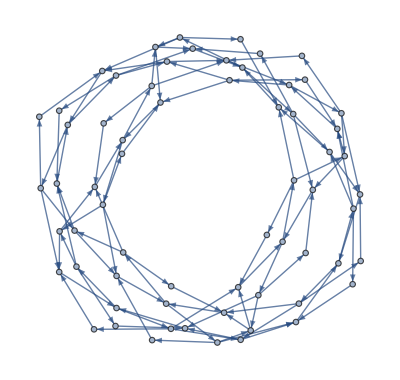

```mathematica
graph=Graph[edges]
```